```mathematica
version=1;
rule={1329, {3, 1}, 1};
rule={20, {2, 1}, 2};
rule=225;
rule={5827733110712,3};
rule={3235313103458,3,1};
```

```mathematica
Clear[StrongAssert]
StrongAssert[test_, messages__]:=If[test, Print[messages]; Quit[4]]
SetAttributes[StrongAssert, HoldRest]
```

```mathematica
helperFile=Import[NotebookDirectory[]<>"kernels/helper.cl"];
templateFile=Import[NotebookDirectory[]<>"kernels/template_v"<>ToString[version]<>".cl"];
```

```mathematica
helperFile
```

#ifdef __APPLE__
inline uint ctz(ulong x)
{
    if (x == 0UL) {
        return 64u;
    }

    return (uint)(63u - clz(x & (~x + 1UL)));
}
#endif

```mathematica
templateFile
```

```mathematica
PointApplyRule[rule_,init_]:=CellularAutomaton[rule, init, 1][[2,(Length[init]+1)/2]]

Clear[AnalyzeRule];
AnalyzeRule[{n_, k_, r_}]:=AnalyzeRule[{n, k, r}]=Module[{rule={n,k, r}},<|
"Rule"->rule, (* may be overrided by a totalistic rule *)
"NormalRule"->rule,  (* always {booleanfunctionnumber, colors, radius} *)
"Colors"->k,
"Radius"->r,
"Totalistic"->False,
"Number"->n,
"Quiescent"->Not[Positive[PointApplyRule[rule, ConstantArray[0, 2r+1]]]],
"Symmetric"->AllTrue[Tuples[Range[0, k-1], 2r+1], PointApplyRule[rule, #]==PointApplyRule[rule, Reverse[#]]&]
|>]

AnalyzeRule[{n_, {k_, 1}, r_}]:=AnalyzeRule[{n, {k, 1}, r}]=With[
{rule={n, {k, 1}, r}},{num=FromDigits[Reverse[PointApplyRule[rule, #]&/@Tuples[Range[0, k-1], 2r+1]], k]},
Join[AnalyzeRule[{num, k, r}],<|"Rule"->rule, "Totalistic"->True|>]
]
AnalyzeRule[{n_, k_}]:=AnalyzeRule[{n, k, 1}]
AnalyzeRule[{n_}]:=AnalyzeRule[{n, 2}]
AnalyzeRule[n_]:=AnalyzeRule[{n}]
```

```mathematica
ar=AnalyzeRule[rule]

n=ar["Number"];
k=ar["Colors"];
r=ar["Radius"];

ArrayPlot[CellularAutomaton[{n, k, r}, {RandomInteger[k-1, 100], 0}, 300], ImageSize->Small]
```

<|Rule→{3235313103458,3,1},NormalRule→{3235313103458,3,1},Colors→3,Radius→1,Totalistic→False,Number→3235313103458,Quiescent→False,Symmetric→False|>

-Graphics-

```mathematica
Clear[SolidColorGoesTo];
SolidColorGoesTo[{n_, k_, r_},color_]:=PointApplyRule[{n, k, r}, ConstantArray[color, 2r+1]]
```

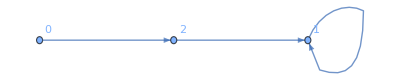

-Graphics-

1

```mathematica
colorCycleGraph=Graph[#->SolidColorGoesTo[{n,k,r}, #]&/@Range[0, k-1], VertexLabels->Automatic]

subgraphWithZeroBackground=Subgraph[colorCycleGraph,SelectFirst[WeaklyConnectedComponents[colorCycleGraph],MemberQ[0]]]

StrongAssert[!AcyclicGraphQ[subgraphWithZeroBackground],"Error: Color sequence contains cycles! ",First[FindCycle[subgraphWithZeroBackground]]];
backgroundcolor=Cases[EdgeList[subgraphWithZeroBackground],x_->x_][[1, 1]]
```

```mathematica
ColorConjugateRule[n_]:=FromDigits[Reverse[1-IntegerDigits[n,2,8]],2]
```

```mathematica
ColorConjugateRuleGeneralized[{n_, k_, r_}, shift_]:={FromDigits[Values[ReverseSort[Thread[Tuples[Range[0, k-1], 2r+1]->Reverse[IntegerDigits[n, k, k^(2r+1)]]]/.i_Integer:>Mod[i-shift, k]]], k],k, r}
```

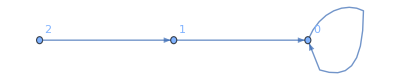

```mathematica
Graph[#->SolidColorGoesTo[ColorConjugateRuleGeneralized[{n,k,r}, backgroundcolor], #]&/@Range[0, k-1], VertexLabels->Automatic]
```

```mathematica
ruleconj=ColorConjugateRuleGeneralized[{n, k, r},backgroundcolor];
```

```mathematica
init=RandomInteger[k-1, 50];
Row[{ArrayPlot[CellularAutomaton[rule, {Mod[init+backgroundcolor, k], Mod[k+backgroundcolor, k]}, 100], ImageSize->Medium],ArrayPlot[CellularAutomaton[ruleconj, {init, 0}, 100], ImageSize->Medium]}]
```

-Graphics--Graphics-

```mathematica
invertedbackgroundcolor=Mod[k-backgroundcolor, k]
```

2

```mathematica
arc=AnalyzeRule[ruleconj]

nc=arc["Number"];
k=arc["Colors"];
r=arc["Radius"];
```

<|Rule→{4243135840083,3,1},NormalRule→{4243135840083,3,1},Colors→3,Radius→1,Totalistic→False,Number→4243135840083,Quiescent→True,Symmetric→False|>

```mathematica
bits=BitLength[k-1]

bfs=BooleanFunction[FromDigits[#, 2]]&/@Echo[Reverse[Transpose[IntegerDigits[#, 2, bits]&/@IntegerDigits[nc, k, k^(2r+1)]]]]
```

2

{{1,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0},{0,1,0,0,0,0,0,1,1,0,1,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0}}

{BooleanFunction[…],BooleanFunction[…]}

```mathematica
BooleanFunction[213413, "ANF"]
```

!((#1&&#2)⊻(#1&&#4)⊻(#1&&#5)⊻(#2&&#4)⊻(#1&&#2&&#3)⊻(#1&&#3&&#4)⊻(#2&&#3&&#5)⊻(#2&&#4&&#5)⊻(#1&&#2&&#3&&#4)⊻(#1&&#2&&#3&&#5)⊻(#1&&#2&&#4&&#5)⊻#3⊻#5)&

```mathematica
MinimalBooleanForm[bf_]:=First[MinimalBy[
Join[
First[BooleanMinimize[bf, #]]&/@{"DNF","CNF","ANF", "NOR", "NAND","AND", "OR"}, FullSimplify[First[BooleanConvert[bf, #]]]&/@{"ESOP", "NOR2", "NAND2", "BDT"}
], 
VertexCount@*ExpressionTree]]
```

```mathematica
MinimalBooleanForm/@bfs
```

{(#4&&((((!#3&&!#5&&#1)||(!#1&&#3))&&#2)||(!#1&&!#2&&!#3)))||(!#2&&#3&&!#4&&!#5),(#1&&#2)⊻(#1&&#3)⊻(#1&&#5)⊻(#2&&#3)⊻(#3&&#4)⊻(#3&&#5)⊻(#1&&#3&&#4)⊻(#1&&#4&&#5)⊻(#2&&#4&&#5)⊻(#1&&#2&&#4&&#5)⊻(#1&&#3&&#4&&#5)⊻#1}